```mathematica
(* use (20) and (21), (17), (18) (66) from https://arxiv.org/pdf/gr-qc/0301090.pdf to compute the entropy of SdS *)


Kh[M_,l_ ] := 1/(√(1-(27 M^2/l^2 )^(1/3)))Abs[M ((2M)/(√(3(M^2/l^2)))Cos[1/3(π+ ArcCos[3 √(3 M^2/l^2)])])^-2-1/l^2(2M)/(√(3(M^2/l^2)))Cos[1/3(π+ ArcCos[3 √(3 M^2/l^2)])]]
```

```mathematica
Kc[M_,l_ ] :=1/(√(1-(27 M^2/l^2 )^(1/3)))Abs[ M ((2M)/(√(3(M^2/l^2)))Cos[1/3(π- ArcCos[3 √(3 M^2/l^2)])])^-2-1/l^2(2M)/(√(3(M^2/l^2)))Cos[1/3(π- ArcCos[3 √(3 M^2/l^2)])]]
```

```mathematica
Ssds[M_,l_] := π/(Kh[M,l])^2+ π/(Kc[M,l])^2+ (2 π)/(Kh[M,l] Kc[M,l])
```

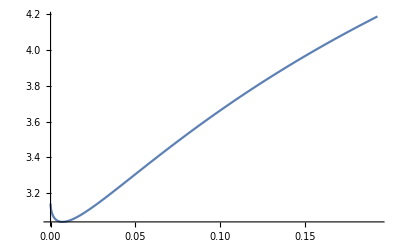

```mathematica
(* Result for Entropy of SdS. Note the strange decrease at small mass *)
Plot[Ssds[M,1],{M,0, √(1/27)}]
```

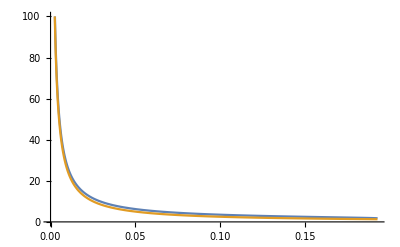

```mathematica
(* Note range of Kh differs from(23) of https://arxiv.org/pdf/gr-qc/0301090.pdf *)

Plot[{Kh[M,1],1/(4M)},{M,0, √(1/27)},PlotRange->{0,100}]
```

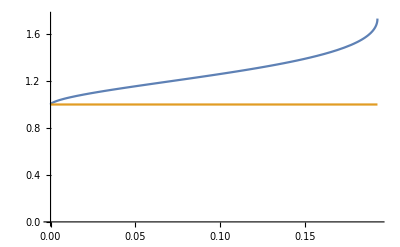

```mathematica
(* Note this range agrees with (24) of https://arxiv.org/pdf/gr-qc/0301090.pdf *)
Plot[{Kc[M,1],1},{M,0, √(1/27)},PlotRange->{0,1.75}]
```

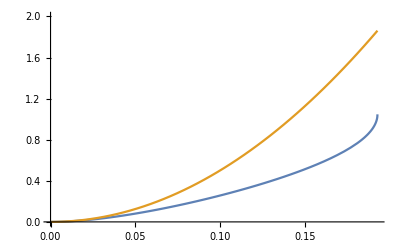

```mathematica
(* Plot contributions to the entropy separately *)

Plot[{π/(Kh[M,1])^2,π/(1/(4M))^2},{M,0, √(1/27)},PlotRange->{0,2}]
```

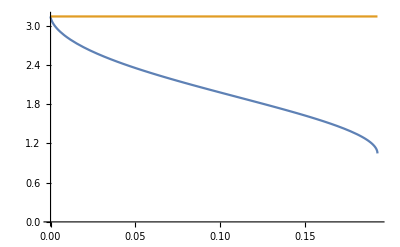

```mathematica
Plot[{π/(Kc[M,1])^2,π/1^2},{M,0, √(1/27)},PlotRange->{0,π}]
```

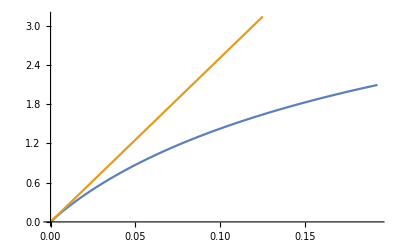

```mathematica
Plot[{(2 π)/(Kh[M,1] Kc[M,1]),(2π)/((1/(4M))1)},{M,0, √(1/27)},PlotRange->{0,π}]
```